```mathematica
ClearAll["Global`*"]
```

```mathematica
<<Notation`
Symbolize[Subscript[K, _]]
```

```mathematica
Subscript[K, Δ]=Triangle@{{0,0},{1,0},{0,1}};
```

```mathematica
∫_({x,y}∈Subscript[K, Δ]) x y
```

1/24

```mathematica
quadrature[weights_List,nodes_List,f_]:=weights.f/@nodes
```

```mathematica
f@{x_,y_}:=3+4y+2x+x^2+10 y^3-x^3+2x y^2+x y-x^2 y+x^4+10x y^3
```

```mathematica
N@∫_({x,y}∈Subscript[K, Δ]) f@{x,y}
```

3.20833

```mathematica
GaussianQuadratureΔ[f_,deg_Integer:3]:=If[deg==1,
quadrature[{ 1/2},{ {1/3,1/3}},f],
If[deg==3,
quadrature[{ (* weights *)
-27/96,25/96,25/96,25/96
},{ (* nodes *)
{1/3,1/3},{1/5,1/5},{1/5,3/5},{3/5,1/5}
},f],
If[deg==4,
quadrature[.5{ (* weights *)
.22338158967801,.22338158967801,.22338158967801,.10995174365532,.10995174365532,.10995174365532
},{ (* nodes *)
{.44594849091597,.44594849091597},
{.44594849091597,.10810301816807},
{.10810301816807,.44594849091597},
{.09157621350977,.09157621350977},
{.09157621350977,.81684757298046},
{.81684757298046,.09157621350977}
},f],
Print["invalid polynomial degree!"]
]
]
]
```

```mathematica
GaussianQuadratureΔ[f,4]
```

3.20833

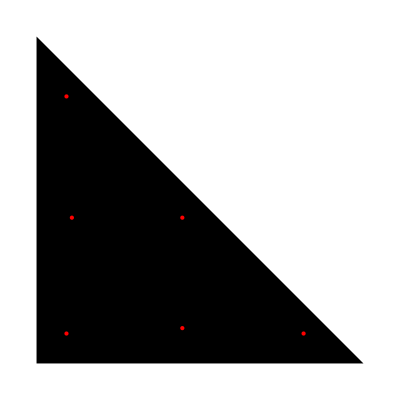

```mathematica
Graphics@{Subscript[K, Δ],Red,Point@{ (* nodes *)
{.44594849091597,.44594849091597},
{.44594849091597,.10810301816807},
{.10810301816807,.44594849091597},
{.09157621350977,.09157621350977},
{.09157621350977,.81684757298046},
{.81684757298046,.09157621350977}
}}
```

```mathematica
ϕ[x_,y_]={1,2,3,4,5,6}.{1,x,y,x y,x^2,y^2};
```

```mathematica
ψ[x_,y_]={11,12,13,14,15,16}.{1,x,y,x y,x^2,y^2};
```

```mathematica
Expand[Grad[ϕ[x,y],{x,y}].Grad[ψ[x,y],{x,y}]]
```

63+274 x+356 x^2+328 y+556 x y+440 y^2

```mathematica
Expand[ϕ[x,y]ψ[x,y]]
```

11+34 x+94 x^2+90 x^3+75 x^4+46 y+120 x y+186 x^2 y+130 x^3 y+121 y^2+198 x y^2+226 x^2 y^2+126 y^3+148 x y^3+96 y^4

```mathematica
∫_({x,y}∈Subscript[K, Δ]) x
```

1/6

```mathematica
.5{ (* weights *)
.22338158967801,.22338158967801,.22338158967801,.10995174365532,.10995174365532,.10995174365532
}
```

{0.111691,0.111691,0.111691,0.0549759,0.0549759,0.0549759}